## Método de la bisección

```mathematica
y[x_]:=x^2-2;
```

```mathematica
x1 = 1;
x2 = 1.5;

intervalos = {{x1,x2}};
Do[
x3 = Mean[{x1,x2}];
If[y[x1]*y[x3]<0,
{x1,x2} = {x1,x3}
,
{x1,x2} = {x3,x2}
];
AppendTo[intervalos,{x1,x2}]; (* Añado {x1,x2} a la lista *)
,
10 (* Número de repeticiones *)
];
```

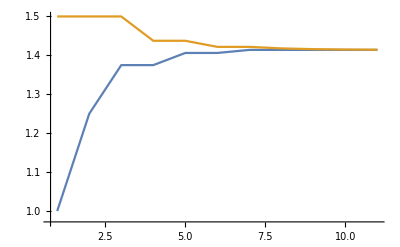

```mathematica
ListLinePlot[Transpose[intervalos],PlotRange->All]
```